{{t1→InterpolatingFunction[{{0., 606.}}, <>],r1→InterpolatingFunction[{{0., 606.}}, <>],φ1→InterpolatingFunction[{{0., 606.}}, <>]}}

Relativistic Solution:

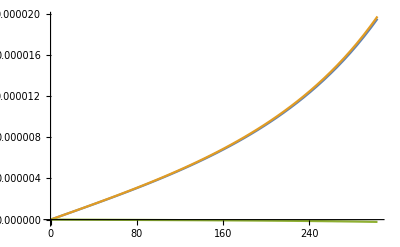

```mathematica
k=1;
Q=1;
q=1;
m=0;
X={t1[λ],r1[λ],φ1[λ]};
g=({{-1, 0, 0}, {0, 1, 0}, {0, 0, r1[λ]^2}});
ℒ1=1/2*(Sum[Sum[g[[a,b]]D[X[[a]],λ]D[X[[b]],λ],{a,3}],{b,3}]/e1[λ]-m^2*e1[λ])+k Q q t1'[λ]/r1[λ];
time=606;
Needs["VariationalMethods`"]
eqs1=EulerEquations[ℒ1,{t1[λ],r1[λ],φ1[λ]},λ]/.{e1[λ]->1,e1'[λ]->0};
s1=NDSolve[{eqs1,t1[0]==0,r1[0]==8,φ1[0]==0,t1'[0]==99 8/(100 64),r1'[0]==0,φ1'[0]==99/(100 64)},{t1,r1,φ1},{λ,0,time},AccuracyGoal->15]

"Relativistic Solution:"
plt=Plot[-100,{x,-10,10},PlotRange->{-10,10},Ticks->None];
Animate[Show[plt,ParametricPlot[{r1[z]Cos[φ1[z]],r1[z]Sin[φ1[z]]}/.s1,{z,0,λ},PlotRange->60,PlotPoints->80],Graphics[{Blue,Ball[{r1[λ]Cos[φ1[λ]],r1[λ]Sin[φ1[λ]]},1/3]}],AspectRatio->Automatic]/.s1,{λ,0.1,time},AnimationRate->time/5, AnimationRunning->False,RefreshRate->120]
"Plot[Sqrt[-t1'[λ]^2+r1'[λ]^2+r1[λ]^2*φ1'[λ]^2]/.s1,{λ,0,time},PlotRange→All]";
Plot[Evaluate[{(r1'[λ] r1''[λ]-t1'[λ] t1''[λ]+r1[λ]^2 φ1'[λ] φ1''[λ])/.s1,(-(r1'[λ] t1'[λ])/r1[λ]^2)/.s1,(r1'[λ] r1''[λ]-t1'[λ] t1''[λ]+r1[λ]^2 φ1'[λ] φ1''[λ]+(r1'[λ] t1'[λ])/r1[λ]^2)/.s1}],{λ,0,time/2},PlotRange->All]
```

```mathematica
k=1;
Q=1;
q=1;
m=0;
ℋ1=Sqrt[m^2+pr[t]^2+pφ[t]^2/r[t]^2]-k Q q/r[t];
time=112;
Needs["VariationalMethods`"]
eqs={pr'[t]==-D[ℋ1,r[t]],r'[t]==D[ℋ1,pr[t]],pφ'[t]==-D[ℋ1,φ[t]],φ'[t]==D[ℋ1,pφ[t]]};
s=NDSolve[{eqs,r[0]==8,φ[0]==0,pr[0]==0,pφ[0]==99/100},{r,φ},{t,0,time},AccuracyGoal->15]

"Massless Solution:"
plt=Plot[-100,{x,-10,10},PlotRange->{-10,10},Ticks->None];
Animate[Show[plt,ParametricPlot[{r[z]Cos[φ[z]],r[z]Sin[φ[z]]}/.s,{z,0,t},PlotRange->60,PlotPoints->80],Graphics[{Blue,Ball[{r[t]Cos[φ[t]],r[t]Sin[φ[t]]},1/3]}],AspectRatio->Automatic]/.s,{t,0.1,time},AnimationRate->time/5, AnimationRunning->False,RefreshRate->120]
"Plot[Sqrt[r'[t]^2+r[t]^2*φ'[t]^2]/.s,{t,0,time},PlotRange→All]";
```

{{r→InterpolatingFunction[{{0., 112.}}, <>],φ→InterpolatingFunction[{{0., 112.}}, <>]}}

Massless Solution:

```mathematica
k=1;
Q=1;
q=1;
m=1;
ℒ2=m/2*(r2'[t]^2+r2[t]^2*φ2'[t]^2)+k Q q/r2[t];
time=400;
Needs["VariationalMethods`"]
eqs2=EulerEquations[ℒ2,{r2[t],φ2[t]},t];
s2=NDSolve[{eqs2,r2[0]==8,φ2[0]==0,r2'[0]==0,φ2'[0]==1/48},{r2,φ2},{t,0,time},AccuracyGoal->10]

"Non-relativistic Solution:"
plt=Plot[-100,{x,-10,10},PlotRange->{-10,10},Ticks->None];
Animate[Show[plt,ParametricPlot[{r2[z]Cos[φ2[z]],r2[z]Sin[φ2[z]]}/.s2,{z,0,t},PlotRange->60,PlotPoints->60],Graphics[{Blue,Ball[{r2[t]Cos[φ2[t]],r2[t]Sin[φ2[t]]},1/3]}],AspectRatio->Automatic]/.s2,{t,0.1,time},AnimationRate->time/5, AnimationRunning->False,RefreshRate->120]
"Plot[Sqrt[r2'[t]^2+r2[t]^2*φ2'[t]^2]/.s2,{t,0,time},PlotRange→All]";
```

{{r2→InterpolatingFunction[{{0., 400.}}, <>],φ2→InterpolatingFunction[{{0., 400.}}, <>]}}

Non-relativistic Solution:

```mathematica
eta={-1,1,1,1};
x={x0[λ],x1[λ],x2[λ],x3[λ]};
xs=Sequence[x0[λ],x1[λ],x2[λ],x3[λ]];
A={A0[xs],A1[xs],A2[xs],A3[xs]};
Simplify[Simplify[Sum[D[x[[u]],λ]D[Sum[eta[[v]]A[[v]]D[x[[v]],λ],{v,1,4}],x[[u]]],{u,1,4}]]/.{x0[λ]->x0,x0'[λ]->v0,x1[λ]->x1,x1'[λ]->v1,x1[λ]->x1,x2'[λ]->v2,x3[λ]->x3,x3'[λ]->v3,Derivative[1,0,0,0][A0][xs]->A00,Derivative[0,1,0,0][A0][xs]->A01,Derivative[0,0,1,0][A0][xs]->A02,Derivative[0,0,0,1][A0][xs]->A03,Derivative[1,0,0,0][A1][xs]->A10,Derivative[0,1,0,0][A1][xs]->A11,Derivative[0,0,1,0][A1][xs]->A12,Derivative[0,0,0,1][A1][xs]->A13,Derivative[1,0,0,0][A2][xs]->A20,Derivative[0,1,0,0][A2][xs]->A21,Derivative[0,0,1,0][A2][xs]->A22,Derivative[0,0,0,1][A2][xs]->A23,Derivative[1,0,0,0][A3][xs]->A30,Derivative[0,1,0,0][A3][xs]->A31,Derivative[0,0,1,0][A3][xs]->A32,Derivative[0,0,0,1][A3][xs]->A33},{-v0^2+v1^2+v2^2+v3^2==0}]
```

-A00 v0^2+(-A01+A10) v0 v1+A11 v1^2+(-A02+A20) v0 v2+(A12+A21) v1 v2+A22 v2^2+(-A03+A30) v0 v3+(A13+A31) v1 v3+(A23+A32) v2 v3+A33 v3^2